# Quantum Chemistry Nolan Hawkins, Morgan Rivers, Julia Rowe, Isabel Yannatos

## Defining functions

#### Generate Hückel Effective Hamiltonian for an Arbitrary Molecule

Using Mathematica’s built-in ChemicalData, we obtain a graphical representation of any hydrocarbon molecule in the the database and create an adjacency matrix for the carbon atoms. The adjacency matrix is converted to a Huckel Matrix. For some molecules this produces numbering of the atoms

```mathematica
generateHuckel[molecule_?StringQ]:=(
carbonLocations={};
tmpCount=0;

(* Append carbon locations *)
Map[Function[{atom},tmpCount++;
If[atom=="C", AppendTo[carbonLocations, tmpCount]]], (* exclude hydrogens *)
ChemicalData[molecule,"VertexTypes"]
];
tmpMatrix=AdjacencyMatrix[Subgraph[Graph[ChemicalData[molecule,"EdgeRules"]],carbonLocations]];

(*
ChemicalData only returns the upper half of the matrix. To represent it as a Huckel,  we put α in the diagonal entries and β to the non-zero entries on the top and bottom.
*)
huckel=β(tmpMatrix+Transpose[tmpMatrix])+α IdentityMatrix[Length[tmpMatrix]];
Return[huckel]
);
```

#### Generate Graph of Molecule with ChemicalData

Similar to preceding function but takes in a molecule string and uses ChemicalData’s “VertexCoordinates” to return a graph for display purposes of the atoms in proper location. As Buckminsterfullerene is at its coolest as a 3D graph and the VertexCoordinates are for 2D display, an exception is made for it.

```mathematica
generateMoleculeGraph[molecule_?StringQ]:=(
carbonLocations={};
tmpCount=0;
Map[Function[{atom},tmpCount++;
If[atom=="C",AppendTo[carbonLocations,tmpCount]]], (* Append if Carbon *)
ChemicalData[molecule,"VertexTypes"]
];

(* If the molecule is Buckminsterfullerene *)
If[molecule=="Buckminsterfullerene",
graph=Subgraph[Graph[ChemicalData[molecule,"EdgeRules"]],carbonLocations],
(* Else, use ChemicalData coordinates *)
graph=Subgraph[Graph[ChemicalData[molecule,"EdgeRules"]],carbonLocations,VertexCoordinates->ChemicalData[molecule,"VertexCoordinates"][[carbonLocations]]]
];
Return[graph];
);
```

#### Calculate Eigenvalues and Eigenvectors from the Huckel matrix

Function that calculates eigenvalues and eigenvectors given a Huckel matrix.
Takes in huckel matrix and returns list of eigenvalues in terms of α and β and a matrix of numerical eigenvectors.

```mathematica
eigens[huckel_?MatrixQ]:=(
eigenSystem=Eigensystem[huckel];
eigenValues=Map[Simplify,eigenSystem⟦1⟧];
eigenVectors=eigenSystem⟦2⟧;
normalizedEigenVectors = Map[Normalize,eigenVectors];
numericEigenVectors=Map[N,normalizedEigenVectors];
Return[{eigenValues,numericEigenVectors}]
);
```

Sorts lists in increasing order of energy and plots energy level diagrams

```mathematica
energyLevelDiagram[eigenList_]:=(
Module[
{eigenVectors,eigenValues},
eigenValues=eigenList⟦1⟧;
eigenVectors=eigenList⟦2⟧;

(*Sort lists in order of increasing energy*)
orderedEigenVectors =Take[eigenVectors⟦Ordering [Map[N, Block[{α = -1, β = -1},eigenValues]]]⟧];
numericEigenValues=Sort[Map[N,Block[{α=-1,β=-1},eigenValues]]];

(* Plot Energy level diagrams *)
Grid[Transpose[{
Map[Text, eigenValues],
Map[Function[{x},ListPlot[x,PlotRange->{-1, 1}, ImageSize->Small, PlotMarkers->{Automatic, Medium}]],
orderedEigenVectors]
}]]
]
)

energyLevelDiagram[eigenList_, index_]:=(
Module[
{eigenVectors,eigenValues},
eigenValues=eigenList⟦1⟧;
eigenVectors=eigenList⟦2⟧;

(*Sort lists in order of increasing energy*)
orderedEigenVectors =Take[eigenVectors⟦Ordering [Map[N, Block[{α = -1, β = -1},eigenValues]]]⟧];
numericEigenValues=Sort[Map[N,Block[{α=-1,β=-1},eigenValues]]];

(* Plot Energy level diagrams *)
Grid[{{Text["Eigenvalue"],Text["Eigenvector"]},{Text[eigenValues⟦index⟧],ListPlot[orderedEigenVectors⟦index⟧,PlotRange->{-1, 1}, ImageSize->Small, PlotMarkers->{Automatic, Small}]
}}]
]
)
```

Calculate Delocalization Energy

Determines the delocalization energy by calculating the energy of the delocalized electrons in the molecule and compairing this with the energy of the double bonds

```mathematica
delocEnergy[eigenList_,molecule_?StringQ]:=(
(* Calculate energy of an isolated carbon-carbon double bond *)
ethylene=({{α, β}, {β, α}});
ethEigen=Eigensystem[ethylene];
ethVals=ethEigen⟦1⟧;
Clear[α, β];
ethEnergy=Block[{α=-1, β=-1},ethVals⟦All⟧];
ethyleneEnergy=Min[ethEnergy];

(* Calculate the energy of the delocalized electrons in the molecule *)
tally=ChemicalData[molecule,"ElementTally"];
numElectrons=tally⟦1⟧⟦2⟧; (*number of carbon atoms*)
eigenValues=eigenList⟦1⟧;

(* Put eigenvalues in ascending order *)
numericEigenValues=Sort[Map[N,Block[{α=-1,β=-1},eigenValues]]]; 
(* Fill the energy levels starting with the lowest *)
moleculeEnergy=Sum[2*numericEigenValues⟦i⟧,{i,Floor[numElectrons/2]}];
(* If an odd number of carbons/electrons add the last one's energy *)
If[Mod[numElectrons,2]==1,moleculeEnergy=moleculeEnergy+numericEigenValues⟦Ceiling[numElectrons/2]⟧,];

bonds=ChemicalData[molecule,"BondTally"];
numDblBonds=bonds⟦1⟧⟦2⟧;
dblBondEnergy=ethyleneEnergy numDblBonds;

(* The difference between the molecule and the isolated double bonds is the delocalization energy *)
Return[moleculeEnergy-dblBondEnergy];
);
```

Calculate Effective Charge Density

Determines the effective charge density at each atom by calculating the probability that a given electron will be found in a given atom

```mathematica
effectiveCharge[eigenList_,numberOfCarbons_,atomNumber_]:=(
(* Calculate the charge density of the delocalized electrons in the molecule *)
eigenVector=eigenList⟦2⟧⟦atomNumber⟧⟦All⟧;

(* Fill the energy levels starting with the lowest, to the highest occupied pi molecular orbital *)
charge=Sum[2*eigenVector⟦i⟧^2,{i,Floor[numberOfCarbons/2]}];
If[Mod[numberOfCarbons,2]==1,charge=charge+eigenVector⟦Ceiling[numberOfCarbons/2]⟧];
Return[charge];
);

effectiveCharge[eigenList_,molecule_?StringQ,atomNumber_]:=(
(* Calculate the charge density of the delocalized electrons in the molecule *)
tally=ChemicalData[molecule,"ElementTally"];
numElectrons=tally⟦1⟧⟦2⟧; (*number of carbon atoms*)
Return[effectiveCharge[eigenList, numElectrons, atomNumber]];
);
```

Calculate Bond Order

Determines the bond order by looking  at the charge denisty of the delocalized electrons

```mathematica
bondOrder[eigenList_,molecule_?StringQ,a1_,a2_]:=(
(* Calculate the charge density of the delocalized electrons in the molecule *)
tally=ChemicalData[molecule,"ElementTally"];
numElectrons=tally⟦1⟧⟦2⟧; (*number of carbon atoms*)
eigenVectors=eigenList⟦2⟧; 
atom1coeffs={};
atom2coeffs={};
(* Order coefficients by atom *)
Do[
AppendTo[atom1coeffs, eigenVectors⟦i⟧⟦a1⟧];
AppendTo[atom2coeffs, eigenVectors⟦i⟧⟦a2⟧], 
{i,Length[eigenVectors]}
]; 

(* Calculate order based on atoms a1 and a2 *)
order=Sum[2*atom1coeffs⟦i⟧*atom2coeffs⟦i⟧,{i,Floor[numElectrons/2]}];
If[Mod[numElectrons,2]==1,order=order+atom1coeffs⟦Ceiling[numElectrons/2]⟧atom2coeffs⟦Ceiling[numElectrons/2]⟧,];
Return[order];
);
```

## Applying these functions to example molecules

Butadiene

```mathematica
ClearAll;
```

The Huckel matrix is defined manually in order to avoid Wolfram’s weird numbering system. We chose to label them 1,2,3,4 along the chain. An α represents the direct integral of an atom, while β represents the resonance integral between two adjacent (bonded) atoms.

```mathematica
butadieneHuckel ={{α, β, 0,0},{β, α,β,0},{0,β,α,β},{0,0,β,α}};
```

Butadiene consists of four carbon atoms with two double bonds between them. The pi orbital overlap causes the pi electrons to be delocalized; they occupy different energy states with some probability of being found at each atom.

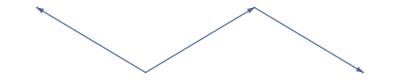

```mathematica
butadieneGraph=generateMoleculeGraph["1,3-Butadiene"]
```

We use the Huckel representation of the Hamiltonian matrix to calculate the eigenvalues (corresponding to energy states) and eigenvectors (corresponding to a probabiltity density of finding a pi electron at a certain atom). Each eigenvalue is shown in the plot with the eigenvectors at atoms 1,2,3, and 4. 
We assume that α and β are both -1.

```mathematica
butadieneEigenList=eigens[butadieneHuckel];
MatrixForm[butadieneEigenList];
```

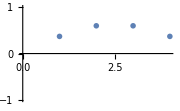
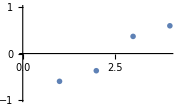
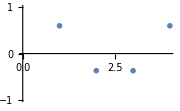
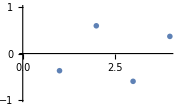
α-1/2 (1+√5) β | -Graphics-
1/2 (2 α+β-√5 β) | -Graphics-
α+1/2 (-1+√5) β | -Graphics-
1/2 (2 α+β+√5 β) | -Graphics-

```mathematica
energyLevelDiagram[butadieneEigenList]
```

From this diagram of the energy states we can see that the lowest energy state (top) has the lowest number of nodes. The sign of the eigenvectors does not change. The node increases by one for each subsequent higher energy state as the sign of the eigenvectors changes more times.

The delocalization energy is the difference between the energy of two isolated double bonds and the energy in butadiene’s delocalized system. The expected value is 0.47β. We’re not sure why the calculated is value is 4 lower than that.

```mathematica
delocEnergy[butadieneEigenList,"1,3-Butadiene"]
```

-4.47214

Calculating the effective charge for the atoms of butadiene confirms that each atom is equivalent.

```mathematica
Table[effectiveCharge[butadieneEigenList,"1,3-Butadiene",i],{i,1,4}]
```

{1.,1.,1.,1.}

Calculating bond order for the three bonds shows that the two outermost bonds are equivalent while the inner bond is more similar to a single bond. This is expected based on the symmetry of the molecule.

```mathematica
Table[bondOrder[butadieneEigenList,"1,3-Butadiene",i,i+1],{i,1,3}]
```

{-0.894427,-0.447214,-0.894427}

In order to visualize the eigenvectors for each eigenstate, we scaled the vertices of our graph representation according to the square of the eigenvector at each atom. Butadiene maintains its symmetry.

```mathematica
butadieneEigenVectors=butadieneEigenList⟦2⟧;
Manipulate[Graph[butadieneGraph, VertexSize->{1->(butadieneEigenVectors⟦i⟧⟦1⟧)^2,2->(butadieneEigenVectors⟦i⟧⟦2⟧)^2,3->(butadieneEigenVectors⟦i⟧⟦3⟧)^2,4->(butadieneEigenVectors⟦i⟧⟦4⟧)^2}, PlotLabel->"The relative size of the atom represens the probability of finding an electron there", ImageSize->Large],{{i,1,"Energy State"},1,4,1}]
```

#### Benzene

```mathematica
ClearAll;
```

```mathematica
huckel=generateHuckel["Benzene"];
```

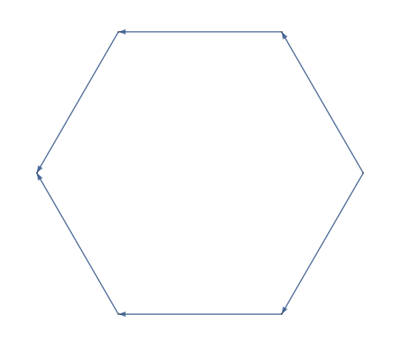

```mathematica
benzeneGraph=generateMoleculeGraph["Benzene"]
```

```mathematica
(*this shows that our manually generated Hamiltonian for Benzene is equivelant to the one generated with our generateHuckel function *)
```

```mathematica
huckel={{α,β,0,0,0,β},{β,α,β,0,0,0},{0,β,α,β,0,0},{0,0,β,α,β,0},{0,0,0,β,α,β},{β,0,0,0,β,α}};
Show[GraphPlot[AdjacencyGraph[Block[{α=0,β=1},huckel]]]];
```

```mathematica
benzeneEigenList=eigens[huckel];
MatrixForm[benzeneEigenList];
```

```mathematica
benzeneEigenvectors=benzeneEigenList⟦2⟧
Manipulate[Graph[benzeneGraph,VertexSize->Table[j->benzeneEigenvectors⟦i⟧⟦j⟧^2, {j,Length[benzeneEigenvectors]}],PlotLabel->"The size of the atom represens the probability of finding an electron there", ImageSize->Large],{{i,1,"Energy State"},1,4,1}]
```

{{-0.408248,0.408248,-0.408248,0.408248,-0.408248,0.408248},{-0.5,0.,0.5,-0.5,0.,0.5},{-0.5,0.5,0.,-0.5,0.5,0.},{0.5,0.,-0.5,-0.5,0.,0.5},{-0.5,-0.5,0.,0.5,0.5,0.},{0.408248,0.408248,0.408248,0.408248,0.408248,0.408248}}

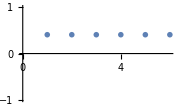
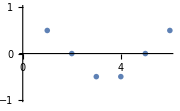
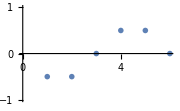
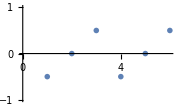
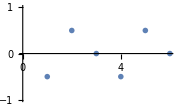
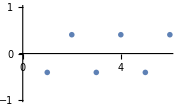
α-2 β | -Graphics-
α-β | -Graphics-
α-β | -Graphics-
α+β | -Graphics-
α+β | -Graphics-
α+2 β | -Graphics-

```mathematica
energyLevelDiagram[benzeneEigenList]
```

```mathematica
delocEnergy[benzeneEigenList,"Benzene"]
```

-8.

Looking at the effective charge of each atom

```mathematica
Table[effectiveCharge[benzeneEigenList,"Benzene",i],{i,1,6}]
```

{1.,1.,1.,1.,1.,1.}

The bond order for all bonds

```mathematica
bondOrder[benzeneEigenList,"Benzene",1,2]
bondOrder[benzeneEigenList,"Benzene",2,3]
bondOrder[benzeneEigenList,"Benzene",3,4]
bondOrder[benzeneEigenList,"Benzene",4,5]
bondOrder[benzeneEigenList,"Benzene",5,6]
bondOrder[benzeneEigenList,"Benzene",6,1]
```

-0.833333

-0.333333

-0.833333

-0.833333

-0.333333

-0.833333

#### Methyl-substituted benzene (Toluene)

Toluene is, surprisingly, not in Wolfram’s database so we have to definte the huckel matrix manually.

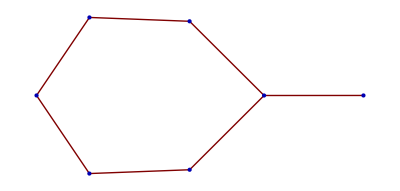

```mathematica
ClearAll;

tolueneHuckel={{α,β,0,0,0,β,0},
             {β,α,β,0,0,0,0},
             {0,β,α,β,0,0,0},
             {0,0,β,α,β,0,0},
             {0,0,0,β,α,β,0},
             {β,0,0,0,β,α,β},
             {0,0,0,0,0,β,α}};
Show[GraphPlot[AdjacencyGraph[Block[{α=0,β=1},tolueneHuckel]]]]
```

Again, we determine the eigenvalues and eigenvectors and represent them by scaling the vertices in the graph.

```mathematica
tolueneEigenList=eigens[tolueneHuckel];
MatrixForm[tolueneEigenList];
```

```mathematica
tolueneEigenVectors=tolueneEigenList⟦2⟧;
Manipulate[AdjacencyGraph[Block[{α=0,β=1},tolueneHuckel],VertexSize->Table[j->(tolueneEigenVectors⟦i⟧⟦j⟧)^2,{j,1,7}], PlotLabel->"The size of the atom represens the probability of finding an electron there", ImageSize->Large],{{i,1,"Energy State"},1,7,1}]
```

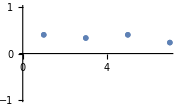
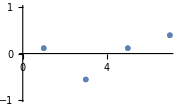
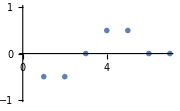
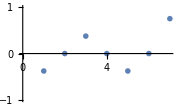
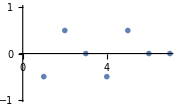
α | -Graphics-
α-β | -Graphics-
α+β | -Graphics-
α-√(3+√2) √(β^2) | -Graphics-
α+√(3+√2) √(β^2) | -Graphics-
α-√(-(-3+√2) β^2) | -Graphics-
α+√(-(-3+√2) β^2) | -Graphics-

```mathematica
energyLevelDiagram[tolueneEigenList]
```

It appears that at the ground state toluene has the highest effective charge at the methyl group, which is surprising given that delocalized electrons in the pi-bond system are expected to be more energetically favorable. The zero effective charge for some atoms shows that delocalized system is disrupted by the methyl substitution. 
The number of nodes does not increase with eigenvalue as it did for butadiene. The number of nodes in each wavefunction is 0,2,2,3,4,2,0.

We also have to redefine the fuctions that depended on the Wolfram database’s information.

TolueneDelocEnergy takes in the list of eigenvalues and eigenvectors calculated above and returns the delocalization energy between toluene and six isolated double bonds.

```mathematica
TolueneDelocEnergy[eigenList_]:=(
(*Calculate energy of an isolated carbon-carbon double bond*)
ethylene=({{α, β}, {β, α}});
ethEigen=Eigensystem[ethylene];
ethVals=ethEigen⟦1⟧;
Clear[α, β];
ethEnergy=Block[{α=-1, β=-1},ethVals⟦All⟧];
ethyleneEnergy=Min[ethEnergy];

(*Calculate the energy of the delocalized electrons in the molecule*)
numElectrons=7; (*number of carbon atoms*)
eigenValues=eigenList⟦1⟧;
(*puts eigenvalues in ascending order*)
numericEigenValues=Sort[Map[N,Block[{α=-1,β=-1},eigenValues]]]; 
(*fill the energy levels starting with the lowest*)
moleculeEnergy=Sum[2*numericEigenValues⟦i⟧,{i,Floor[numElectrons/2]}];
(*in case there's an odd number of carbons/electrons*)
If[Mod[numElectrons,2]==1,moleculeEnergy=moleculeEnergy+numericEigenValues⟦Ceiling[numElectrons/2]⟧,];

numDblBonds=6;
dblBondEnergy=ethyleneEnergy numDblBonds;

(*The difference between the molecule and the isolated double bonds is the delocalization energy*)
Return[moleculeEnergy-dblBondEnergy];
);
```

```mathematica
TolueneDelocEnergy[tolueneEigenList]
```

-3.72057

The results is higher than the delocalization energy of benzene, suggesting that the methyl substitution is energetically unfavorable.

TolueneEffectiveCharge takes in the list of eigenpairs and the label of a certain atom and returns the effective charge density at that atom.

```mathematica
TolueneEffectiveCharge[eigenList_,atomNumber_]:=(
(*Calculate the charge density of the delocalized electrons in the molecule*)
numElectrons=7; (*number of carbon atoms*)
eigenVector=eigenList⟦2⟧⟦atomNumber⟧⟦All⟧;
(*fill the energy levels starting with the lowest, to the highest occupied pi molecular orbital*)
Block[{α=-1, β=-1},
charge=Sum[2*eigenVector⟦i⟧^2,{i,Floor[numElectrons/2]}];
If[Mod[numElectrons,2]==1,charge=charge+eigenVector⟦Ceiling[numElectrons/2]⟧];
];
Return[charge];
);
```

```mathematica
Table[TolueneEffectiveCharge[tolueneEigenList,i],{i,1,7}]
```

{0.571429,0.5,1.5,1.16019,0.453082,0.554097,1.2612}

Unlike benzene, the atoms are not all equivalent because the symmetry has been disrupted.

TolueneBondOrder takes in the list of eigenpairs and the labels of two adjacent atoms and returns the bond order between them.

```mathematica
TolueneBondOrder[eigenList_,a1_,a2_]:=(
(*Calculate the charge density of the delocalized electrons in the molecule*)
numElectrons=7; (*number of carbon atoms*)
eigenVectors=eigenList⟦2⟧; 
Block[{α=-1,β=-1},
atom1coeffs=eigenList⟦2⟧⟦a1⟧⟦All⟧;
atom2coeffs=eigenList⟦2⟧⟦a2⟧⟦All⟧;
(*calculate order for a bond a1 a2*)
order=Sum[2*atom1coeffs⟦i⟧*atom2coeffs⟦i⟧,{i,Floor[numElectrons/2]}];
If[Mod[numElectrons,2]==1,order=order+atom1coeffs⟦Ceiling[numElectrons/2]⟧atom2coeffs⟦Ceiling[numElectrons/2]⟧];];
Return[order];
);
TolueneBondOrder[tolueneEigenList,1,2]
TolueneBondOrder[tolueneEigenList,2,3]
TolueneBondOrder[tolueneEigenList,3,4]
TolueneBondOrder[tolueneEigenList,4,5]
TolueneBondOrder[tolueneEigenList,5,6]
TolueneBondOrder[tolueneEigenList,6,1]
TolueneBondOrder[tolueneEigenList,6,7]
```

0.377964

-0.25

-0.583037

0.181635

0.0915266

-0.512377

0.28265

As expected, the bonds are not all the same order because the molecule is asymmetric.

#### Naphthalene

```mathematica
ClearAll;
molecule="Naphthalene";
naphthaleneHuckel=generateHuckel["Naphthalene"];
```

Naphthalene is like two benzene molecules with one shared bond.

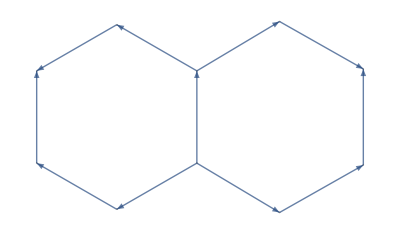

```mathematica
naphthaleneGraph=generateMoleculeGraph["Naphthalene"]
```

```mathematica
naphthaleneEigenList=eigens[naphthaleneHuckel];
MatrixForm[naphthaleneEigenList];
```

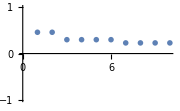
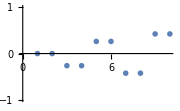
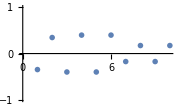
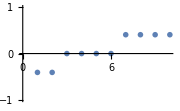
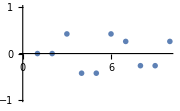
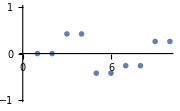
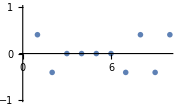
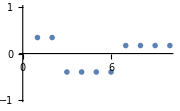
α-β | -Graphics-
α+β | -Graphics-
α-1/2 (1+√5) β | -Graphics-
1/2 (2 α+β-√5 β) | -Graphics-
α+1/2 (-1+√5) β | -Graphics-
1/2 (2 α+β+√5 β) | -Graphics-
α-1/2 (1+√13) β | -Graphics-
1/2 (2 α+β-√13 β) | -Graphics-
α+1/2 (-1+√13) β | -Graphics-
1/2 (2 α+β+√13 β) | -Graphics-

```mathematica
energyLevelDiagram[naphthaleneEigenList]
```

The number of nodes for each wavefunction is 0, 3, 9, 1, 4, 2, 4, 2, 5, 7.

```mathematica
naphthaleneEigenVectors=naphthaleneEigenList⟦2⟧;
Manipulate[AdjacencyGraph[Block[{α=0,β=1},naphthaleneHuckel],VertexSize->Table[j->(naphthaleneEigenVectors⟦i⟧⟦j⟧)^2,{j,1,10}], PlotLabel->"The size of the atom represents the relative probability of finding an electron there", ImageSize->Large],{{i,1,"Energy State"},1,10,1}]
```

The molecule maintains its symmetry around the shared bond but has disruptions to the delocalization for some energy states.

To visualize the effective charge at each atom, we also created a graph whose vertices’ radii are proprtional to the effective charge. This showed transverse symmetry about the central bond.

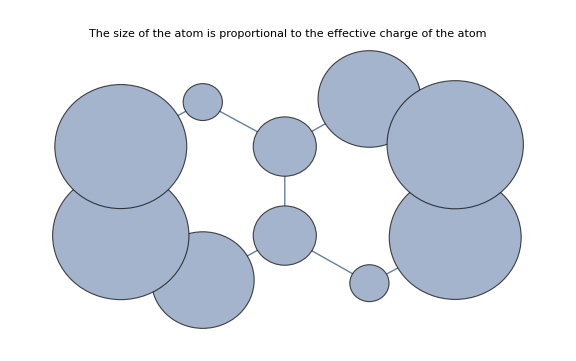

-Graphics-

```mathematica
Graph[naphthaleneGraph, VertexSize->Table[j-> effectiveCharge[naphthaleneEigenList,"Naphthalene",j],{j,VertexCount[naphthaleneGraph]}], PlotLabel->"The size of the atom is proportional to the effective charge of the atom", ImageSize->Large]
```

```mathematica
naphthaleneDelocEnergy = delocEnergy[naphthaleneEigenList,"Naphthalene"]
```

-13.6832

The delocalization energy is lower than that of benzene, suggesting that there is more extensive delocalization in naphthalene.

#### Buckminsterfullerene

```mathematica
ClearAll;
molecule="Buckminsterfullerene";
buckyHuckel=generateHuckel["Buckminsterfullerene"];
buckyGraph=UndirectedGraph[generateMoleculeGraph["Buckminsterfullerene"]];
GraphPlot3D[buckyGraph]
```

-Graphics3D-

Buckminsterfullerene is a 60-carbon molecule in the form of a truncated icosahedron.

```mathematica
buckyEigenList=eigens[Block[{α=-1, β=-1},buckyHuckel] // N];
MatrixForm[buckyEigenList];
```

```mathematica
Length[buckyEigenList⟦1⟧]
```

60

We again visualize the energy levels and eigenvectors on a plot and on the molecule itself.

```mathematica
Manipulate[energyLevelDiagram[buckyEigenList, i],{{i,1,"Energy State"},1,Length[buckyEigenList⟦1⟧],1}]
```

```mathematica
buckyEigenvectors=buckyEigenList⟦2⟧;
Manipulate[Graph3D[buckyGraph,VertexSize->Table[j->buckyEigenvectors⟦i⟧⟦j⟧^2*10, {j,Length[buckyEigenvectors⟦1⟧]}],PlotLabel->"The size of the atom represens the probability of finding an electron there", ImageSize->Large],{{i,1,"Energy State"},1,60,1}]
```

The following plot shows a bucky ball graph with the sizes of the vertexes proportional to the square of the effective charge. Squaring the values makes the differences more readily apparent.

```mathematica
Graph3D[buckyGraph, VertexSize->Table[j-> effectiveCharge[buckyEigenList,"Buckminsterfullerene",j]^2,{j,VertexCount[buckyGraph]}], ImageSize->Large]
```

-Graphics3D-

#### Hückel Effective Hamiltonian generator for Graphene

Given a width and a height (in number of strips of benzene rings) and a type (by default “Armchair”, the other option is “Zigzag”), the graphene[ ] function generates a graph of a corresponding strip of Graphene and the Hückel Effective Hamiltonian for that graphene.

The graphene[ ] function is helped by the functions armchairGrapheneLocation[ ], armchairGrapheneEdges[ ], zigzagGrapheneLocation[ ], and zigzagGrapheneEdges[ ], which, when given the x and y index of the atom in a grid of a specified width and height, will return the coordinate of the atom or the bonds that the atom is connected to given the type of graphene.

Get a coordinate for an atom enumerated (x, y) in an armchair strip of graphene

```mathematica
armchairGrapheneLocation[x_,y_]:=
Module[{},
x=x-1;
y=y-1;
If[EvenQ[x],
If[EvenQ[y],
Return[{(1.5 x+.5), (√3)/2 y }],
Return[{1.5 x , (√3)/2 y}]
],
If[OddQ[y],
Return[{(1.5 x+.5), (√3)/2 y }],
Return[{1.5 x, (√3)/2 y }]
]
]]
```

Get a coordinate for an atom enumerated (x, y) in a zigzag strip of graphene

```mathematica
zigzagGrapheneLocation[x_,y_]:=Reverse[armchairGrapheneLocation[y,x]]
```

Get a list of edges or bonds for an atom enumerated (x, y) in an armchair strip of graphene of a given  width and height

```mathematica
armchairGrapheneEdges[x_,y_, width_, height_]:=Module[{edges, index},
index=(x-1) height+y;
edges={};
If[x<width && Mod[x,2]==Mod[y,2],AppendTo[edges, index+height]];
If[y<height, AppendTo[edges, index+1]];
Table[UndirectedEdge[index, edges⟦i⟧],{i, 1, Length[edges]}]
]
```

Get a list of edges or bonds for an atom enumerated (x, y) in a zigzag strip  of graphene of a given width and height

```mathematica
zigzagGrapheneEdges[x_,y_, width_, height_]:=Module[{edges, index},
index=(x-1) height+y;
edges={};
If[x<width ,AppendTo[edges, index+height]];
If[y<height&& Mod[x,2]==Mod[y,2], AppendTo[edges, index+1]];
Table[UndirectedEdge[index, edges⟦i⟧],{i, 1, Length[edges]}]
]
```

Graphene hamiltonian generator function

```mathematica
graphene[width_, height_, type_:"Armchair"]:=Module[
{columnHeight, totalAtoms, atomLocations, atomConnections, graph, huckel},

If[type=="Armchair",

columnHeight=2 height+1;
totalAtoms=2 width(columnHeight);
atomLocations=Flatten[Array[armchairGrapheneLocation,{2 width, 2 height+1}],1];
atomConnections=Flatten[Array[Function[{x,y},armchairGrapheneEdges[x,y,2 width, 2 height+1]], {2 width, columnHeight}],2];
graph=Graph[Range[totalAtoms],atomConnections, VertexCoordinates->atomLocations],

(* else, for zigzag *)
totalAtoms=2 height(2 width+1);
atomLocations=Flatten[Array[zigzagGrapheneLocation, {2 width+1, 2 height}],1];
atomConnections=Flatten[Array[Function[{x,y},zigzagGrapheneEdges[x,y,2 width+1, 2 height]], {2 width+1, 2 height}],2];
graph=Graph[Range[totalAtoms],atomConnections, VertexCoordinates->atomLocations];
];
Return[<|"Graph"->graph,"Huckel"->α IdentityMatrix[totalAtoms]+β AdjacencyMatrix[graph]|>]
]
```

#### Zigzag

Set::setraw: Cannot assign to raw object 1.

Set::setraw: Cannot assign to raw object 2.

General::stop: Further output of Set :: setraw will be suppressed during this calculation.

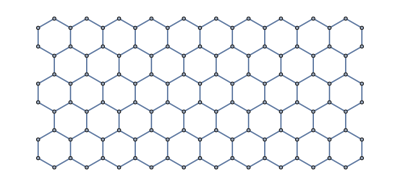

```mathematica
zigzagData=graphene[10,3, "Zigzag"];
zigzagData["Graph"]
zigzagEigenList=Eigensystem[Block[{α=0, β=-1},zigzagData["Huckel"]] // N];
```

Visualizing the eigenvectors:

```mathematica
Manipulate[energyLevelDiagram[zigzagEigenList, i],{{i,1,"Energy State"},1,Length[zigzagEigenList⟦1⟧],1}]
```

To visualize the eigenvectors we look at the magnitude of the eigenvectors for a given energy level

```mathematica
zigzagEigenvectors=zigzagEigenList⟦2⟧;
Manipulate[Graph[zigzagData["Graph"],VertexSize->Table[j->zigzagEigenvectors⟦i⟧⟦j⟧^2*30, {j,Length[zigzagEigenvectors⟦1⟧]}],PlotLabel->"The size of the atom represens the probability of finding an electron there", ImageSize->Large],{{i,1,"Energy State"},1,Length[zigzagEigenvectors⟦1⟧],1}]
```

Here we examine the effective charge of each atom for the first eigenstate

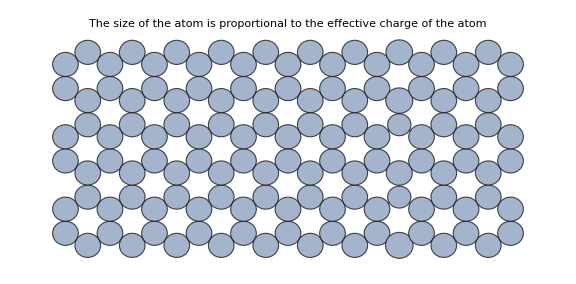

```mathematica
Graph[zigzagData["Graph"],VertexSize->Table[j->effectiveCharge[zigzagEigenList,Length[zigzagEigenvectors⟦1⟧],j], {j,Length[zigzagEigenvectors⟦1⟧]}],PlotLabel->"The size of the atom is proportional to the effective charge of the atom", ImageSize->Large]
```

#### Armchair

Set::setraw: Cannot assign to raw object 1.

General::stop: Further output of Set :: setraw will be suppressed during this calculation.

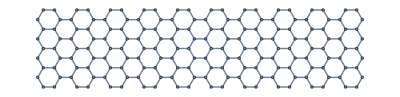

```mathematica
armchairData=graphene[10,4, "Armchair"];
armchairData["Graph"]
armchairEigenList=Eigensystem[Block[{α=0, β=-1},armchairData["Huckel"]] // N];
```

Visualizing the eigenvectors :

```mathematica
Manipulate[energyLevelDiagram[armchairEigenList, i],{{i,1,"Energy State"},1,Length[armchairEigenList⟦1⟧],1}]
```

To visualize the eigenvectors we look at the magnitude of the eigenvectors for a given energy level

```mathematica
armchairEigenvectors=armchairEigenList⟦2⟧;
Manipulate[Graph[armchairData["Graph"],VertexSize->Table[j->armchairEigenvectors⟦i⟧⟦j⟧^2*30, {j,Length[armchairEigenvectors⟦1⟧]}],PlotLabel->"The size of the atom represens the probability of finding an electron there", ImageSize->Large],{{i,1,"Energy State"},1,Length[armchairEigenvectors⟦1⟧],1}]
```

We see that these are unsurprisingly 90 degree rotations of the corresponding zigzag states, however, we know that states such as the last one are not physically realizable as these strips continue to infinity.  Through these plots we do see the difference in the edge state of the two different configurations.

Here we examine the effective charge of each atom for the first eigenstate

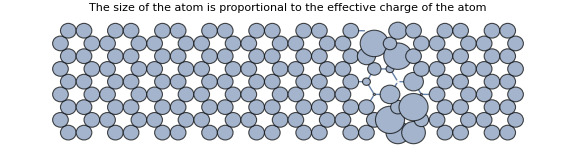

```mathematica
Graph[armchairData["Graph"],VertexSize->Table[j->effectiveCharge[armchairEigenList,Length[armchairEigenvectors⟦1⟧],j], {j,Length[armchairEigenvectors⟦1⟧]}],PlotLabel->"The size of the atom is proportional to the effective charge of the atom", ImageSize->Large]
```